```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin hourly price: Recent (≥2020) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2025 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2025-12-31

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2018-05-15

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2026-01-01,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

66743

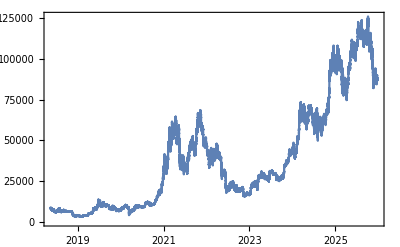

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/bitcoin-bubbles/csv/Bitcoin_price-hourly-20250301-20251225.csv

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

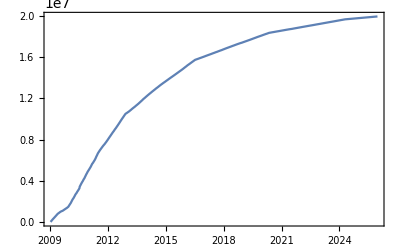

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1766354262}

```mathematica
{hourlyPrices[[1]][[1]],hourlyPrices[[-1]][[1]]}
```

{1526364000,1766707200}

```mathematica
{supplyFunction[hourlyPrices[[1]][[1]]], supplyFunction[hourlyPrices[[-3]][[1]]]}
```

{1.70344×10^7,1.99671×10^7}

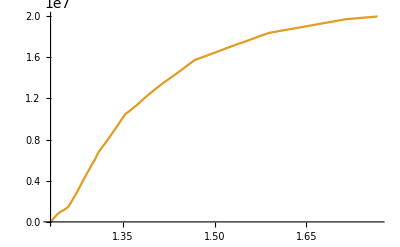

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPrices
```

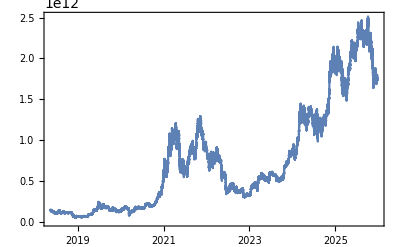

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2025 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-03-11", "2025-07-30"},{"2025-04-07", "2025-10-07"}}
```

{{2025-03-11,2025-07-30},{2025-04-07,2025-10-07}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1741647600,1753830000},{1743980400,1759791600}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{141,183}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1741647600,28.0746},{1743980400,28.0724}}

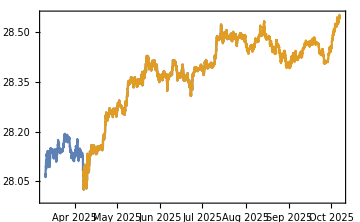

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.125,0.920572},{1.00114,0.979106}}

```mathematica
Length/@bubblesScaled
```

{3365,4373}

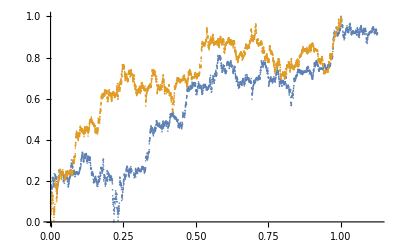

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/bitcoin-bubbles/csv/bubbleScaled-1.tsv,/Users/mauro/Projects/bitcoin-bubbles/csv/bubbleScaled-2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.1
```

0.1

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{15.728,3344.28},{15.7491,4352.25}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{3.49667,0.0323397,0.00210422},{4.00928,0.0303544,0.00323111}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

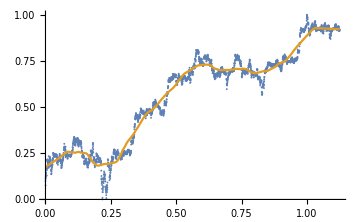
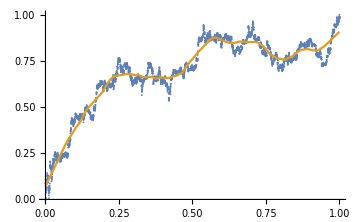

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

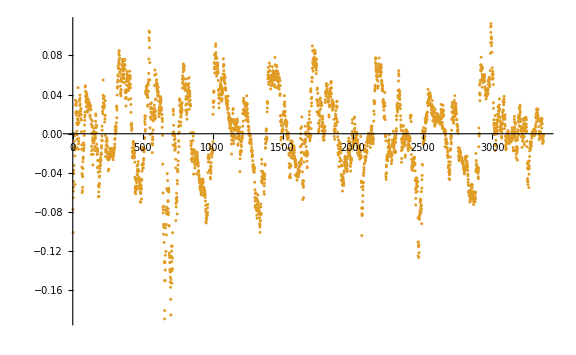
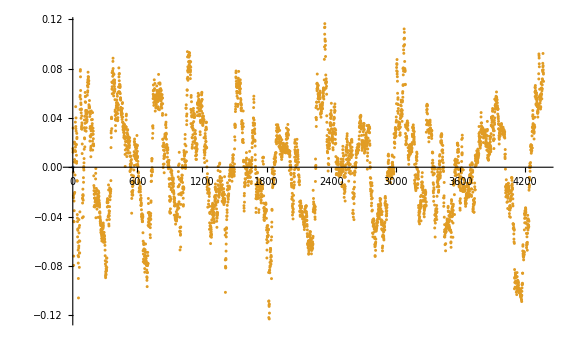

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0405951,0.0398375}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{5.5441,6.94074}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{5.5441 > 3.49667,6.94074 > 4.00928}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0406856,0.0399114}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0406856 > 0.0323397,0.0399114 > 0.0303544}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0323111,0.0303338}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0407159,0.0399343}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0407159 > 0.0323397,0.0399343 > 0.0303544}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0323353,0.0303512}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

1

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{15.728,3344.28}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.125

2.55053

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0212766

```mathematica
(* Define 5 days resolution scaled initial time step *)
stepTi=5/bubblesDays[[bubble]]//N
```

0.035461

```mathematica
(* Slow. Shortcut below *)
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{9817.12,{{a→1.09612,b→-0.675578,c→-0.161472,d→-0.0428971,T_1→0.,tc→1.23148,m→0.7,ω→5.5,RSS→10.7154,ℛerror→0.00319101,ℛσ→0.0564386,LL→11256.1,ρ→0.988126,σ→-0.00867039,μ→-1.51303×10^-18},{a→1.1772,b→-0.591805,c→0.114098,d→-0.0586029,T_1→0.035461,tc→1.55063,m→1.,ω→10.,RSS→7.60836,ℛerror→0.00234031,ℛσ→0.0483322,LL→10971.,ρ→0.984928,σ→-0.00835844,μ→1.31481×10^-18},{a→1.20139,b→-0.590626,c→0.125205,d→-0.00137289,T_1→0.070922,tc→1.59319,m→1.,ω→10.7,RSS→7.36776,ℛerror→0.00234343,ℛσ→0.0483629,LL→10618.3,ρ→0.98508,σ→-0.0083218,μ→1.10017×10^-17},{a→1.2429,b→-0.595436,c→0.0858615,d→0.0808835,T_1→0.106383,tc→1.65701,m→1.,ω→11.6,RSS→7.40904,ℛerror→0.00243879,ℛσ→0.0493354,LL→10249.9,ρ→0.985404,σ→-0.00839702,μ→4.34782×10^-19},{a→1.19104,b→-0.610915,c→0.119398,d→-0.050621,T_1→0.141844,tc→1.55063,m→1.,ω→10.,RSS→6.30605,ℛerror→0.0021515,ℛσ→0.0463369,LL→9876.8,ρ→0.983354,σ→-0.00841786,μ→2.9274×10^-18},{a→1.19704,b→-0.619275,c→0.121918,d→-0.0475922,T_1→0.177305,tc→1.55063,m→1.,ω→10.,RSS→6.14282,ℛerror→0.00217522,ℛσ→0.0465898,LL→9509.8,ρ→0.983327,σ→-0.00847074,μ→-4.03895×10^-18},{a→1.10225,b→-0.666997,c→-0.0522134,d→-0.168984,T_1→0.212766,tc→1.35914,m→1.,ω→7.2,RSS→4.89773,ℛerror→0.00180196,ℛσ→0.0424027,LL→9199.29,ρ→0.980486,σ→-0.00833431,μ→7.47008×10^-18},{a→1.02896,b→-0.701792,c→-0.163583,d→-0.144928,T_1→0.248227,tc→1.23148,m→1.,ω→5.4,RSS→4.05956,ℛerror→0.00155479,ℛσ→0.0393856,LL→9139.49,ρ→0.982041,σ→-0.00742945,μ→-3.42724×10^-18},{a→1.0342,b→-0.718184,c→-0.161469,d→-0.159351,T_1→0.283688,tc→1.23148,m→1.,ω→5.3,RSS→3.9856,ℛerror→0.0015841,ℛσ→0.0397534,LL→8850.88,ρ→0.983203,σ→-0.00725412,μ→-5.76222×10^-18},{a→1.0253,b→-0.690531,c→-0.156396,d→-0.140676,T_1→0.319149,tc→1.23148,m→1.,ω→5.4,RSS→3.79292,ℛerror→0.00156862,ℛσ→0.0395568,LL→8500.87,ρ→0.982363,σ→-0.00739502,μ→4.76252×10^-18},{a→1.10339,b→-0.683751,c→-0.115748,d→-0.104912,T_1→0.35461,tc→1.27404,m→0.8,ω→6.1,RSS→3.36573,ℛerror→0.00145639,ℛσ→0.0381133,LL→8156.71,ρ→0.98214,σ→-0.0071695,μ→-1.32503×10^-18},{a→1.04153,b→-0.69676,c→-0.143022,d→-0.149383,T_1→0.390071,tc→1.25276,m→1.,ω→5.6,RSS→3.20985,ℛerror→0.00145638,ℛσ→0.0381107,LL→7775.84,ρ→0.982014,σ→-0.00719395,μ→1.22546×10^-17},{a→1.04221,b→-0.698896,c→-0.155659,d→-0.140919,T_1→0.425532,tc→1.25276,m→1.,ω→5.7,RSS→3.15081,ℛerror→0.00150182,ℛσ→0.038698,LL→7394.36,ρ→0.982481,σ→-0.00721023,μ→-5.06913×10^-18},{a→1.03847,b→-0.645145,c→-0.131158,d→-0.129539,T_1→0.460993,tc→1.27404,m→1.,ω→6.2,RSS→2.81834,ℛerror→0.00141554,ℛσ→0.0375671,LL→7007.27,ρ→0.980395,σ→-0.0074005,μ→4.96984×10^-18},{a→1.16962,b→-0.7103,c→-0.0873253,d→-0.0926857,T_1→0.496454,tc→1.25276,m→0.6,ω→5.7,RSS→2.5254,ℛerror→0.00134045,ℛσ→0.036554,LL→6638.97,ρ→0.98023,σ→-0.00723076,μ→6.10544×10^-19},{a→1.06957,b→-0.667538,c→-0.109673,d→-0.126628,T_1→0.531915,tc→1.23148,m→0.8,ω→5.3,RSS→2.46851,ℛerror→0.00138837,ℛσ→0.0371981,LL→6278.,ρ→0.981137,σ→-0.00718882,μ→6.68142×10^-18}}}

```mathematica
(* Shortcut: *)
fits={9817.119937,{{a->1.0961232681028883,b->-0.6755775661498205,c->-0.16147234072198888,d->-0.042897068430523565,Subscript[T, 1]->0.,tc->1.2314829787234043,m->0.7000000000000001,ω->5.5,RSS->10.71541550859125,ℛerror->0.003191011169919967,ℛσ->0.056438636688300764,LL->11256.100287054638,ρ->0.9881256619318879,σ->-0.008670389226309102,μ->-1.5130275641931332*^-18},{a->1.177201090032938,b->-0.5918054438942789,c->0.11409801832918783,d->-0.05860285682580871,Subscript[T, 1]->0.03546099290780142,tc->1.550631914893617,m->1.,ω->10.,RSS->7.608360142541265,ℛerror->0.002340313793460863,ℛσ->0.048332209757186426,LL->10970.969994454004,ρ->0.9849281937452495,σ->-0.008358436405106157,μ->1.3148142970038792*^-18},{a->1.2013908286132575,b->-0.5906261107227775,c->0.1252050278920656,d->-0.001372887774372608,Subscript[T, 1]->0.07092198581560284,tc->1.5931851063829787,m->1.,ω->10.7,RSS->7.367759112302417,ℛerror->0.0023434348321572573,ℛσ->0.04836291085907323,LL->10618.326375124449,ρ->0.9850799635861056,σ->-0.008321803409154201,μ->1.1001690833425011*^-17},{a->1.2429037640362002,b->-0.5954356934580521,c->0.08586145680792806,d->0.08088351421463112,Subscript[T, 1]->0.10638297872340427,tc->1.6570148936170213,m->1.,ω->11.6,RSS->7.4090375202188214,ℛerror->0.0024387878605065245,ℛσ->0.04933539083161452,LL->10249.925540854236,ρ->0.9854042315018102,σ->-0.008397020305201052,μ->4.347824003041196*^-19},{a->1.1910364763013692,b->-0.6109152524247783,c->0.11939825102855577,d->-0.05062096124923706,Subscript[T, 1]->0.14184397163120568,tc->1.550631914893617,m->1.,ω->10.,RSS->6.306052577661975,ℛerror->0.0021515020735796576,ℛσ->0.04633688345169166,LL->9876.796560042532,ρ->0.9833544930752475,σ->-0.008417857760612364,μ->2.9273984804874025*^-18},{a->1.1970368924754902,b->-0.6192751882449413,c->0.12191803852414575,d->-0.04759215260820066,Subscript[T, 1]->0.1773049645390071,tc->1.550631914893617,m->1.,ω->10.,RSS->6.1428226149988925,ℛerror->0.002175220472733319,ℛσ->0.04658979177759289,LL->9509.797652685565,ρ->0.9833267353008923,σ->-0.008470743050048976,μ->-4.038951207568113*^-18},{a->1.1022459693219975,b->-0.6669973563284239,c->-0.05221341186291904,d->-0.16898419293772066,Subscript[T, 1]->0.21276595744680854,tc->1.3591425531914894,m->1.,ω->7.2,RSS->4.8977327907740795,ℛerror->0.0018019620275106988,ℛσ->0.04240274694114702,LL->9199.289761195843,ρ->0.9804863402208778,σ->-0.008334308659196137,μ->7.470083564345615*^-18},{a->1.028962980611383,b->-0.7017921302778101,c->-0.1635829150103105,d->-0.14492839462981089,Subscript[T, 1]->0.24822695035460995,tc->1.2314829787234043,m->1.,ω->5.4,RSS->4.059563661030897,ℛerror->0.0015547926698701255,ℛσ->0.03938563182532495,LL->9139.494150647515,ρ->0.9820406251877614,σ->-0.007429451297163495,μ->-3.4272384037391866*^-18},{a->1.0341963472116933,b->-0.7181843293320589,c->-0.16146925046039545,d->-0.15935117646698785,Subscript[T, 1]->0.28368794326241137,tc->1.2314829787234043,m->1.,ω->5.300000000000001,RSS->3.9856039476401093,ℛerror->0.001584103317821983,ℛσ->0.039753422925257985,LL->8850.882475791108,ρ->0.9832032579420489,σ->-0.007254117485320214,μ->-5.762220360604258*^-18},{a->1.0253007801348402,b->-0.6905311773616879,c->-0.15639582117258696,d->-0.14067568653250404,Subscript[T, 1]->0.3191489361702128,tc->1.2314829787234043,m->1.,ω->5.4,RSS->3.7929236430749196,ℛerror->0.0015686201997828452,ℛσ->0.039556762715319056,LL->8500.868020681017,ρ->0.9823626350857887,σ->-0.007395023872246389,μ->4.7625215690494605*^-18},{a->1.1033875185476076,b->-0.6837506390225847,c->-0.11574813743835034,d->-0.10491235774507149,Subscript[T, 1]->0.3546099290780142,tc->1.2740361702127658,m->0.8,ω->6.1,RSS->3.365728702059887,ℛerror->0.0014563949381479389,ℛσ->0.03811329850176256,LL->8156.712860754301,ρ->0.9821401363211687,σ->-0.007169503564369514,μ->-1.3250319659676393*^-18},{a->1.0415288899921877,b->-0.6967602958454844,c->-0.14302248260064462,d->-0.14938315702902155,Subscript[T, 1]->0.3900709219858156,tc->1.252759574468085,m->1.,ω->5.6,RSS->3.209853268506748,ℛerror->0.0014563762561282884,ℛσ->0.038110658528054425,LL->7775.84464132056,ρ->0.9820141434884604,σ->-0.007193945701526393,μ->1.2254637076201444*^-17},{a->1.0422060999632876,b->-0.698895656105544,c->-0.1556594121492297,d->-0.14091930260558702,Subscript[T, 1]->0.4255319148936171,tc->1.252759574468085,m->1.,ω->5.7,RSS->3.1508084471284663,ℛerror->0.0015018152750850648,ℛσ->0.038697965475011295,LL->7394.360823229328,ρ->0.9824805800062496,σ->-0.007210232736834581,μ->-5.069132661040294*^-18},{a->1.0384691169030469,b->-0.6451450196003391,c->-0.13115799453245164,d->-0.12953936633573726,Subscript[T, 1]->0.4609929078014185,tc->1.2740361702127658,m->1.,ω->6.2,RSS->2.8183429954823036,ℛerror->0.0014155414341950295,ℛσ->0.03756711900567744,LL->7007.267330078856,ρ->0.9803947441783099,σ->-0.007400504387831479,μ->4.969841525221677*^-18},{a->1.1696187134526033,b->-0.7103003478194206,c->-0.08732530841912588,d->-0.09268565295851867,Subscript[T, 1]->0.4964539007092199,tc->1.252759574468085,m->0.6,ω->5.7,RSS->2.525404327832807,ℛerror->0.001340448157023783,ℛσ->0.03655397059211363,LL->6638.974928436158,ρ->0.9802297425298354,σ->-0.00723075502369218,μ->6.105437225950212*^-19},{a->1.069567950096914,b->-0.6675379339011334,c->-0.109673044833946,d->-0.1266280898244371,Subscript[T, 1]->0.5319148936170213,tc->1.2314829787234043,m->0.8,ω->5.300000000000001,RSS->2.468513003615439,ℛerror->0.001388365018906321,ℛσ->0.03719805949010352,LL->6278.002306742909,ρ->0.9811373379098449,σ->-0.007188816256808454,μ->6.681419227620749*^-18}}};
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

163.619

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.23148 | ℛσ→0.0564386 | LL→11256.1
T_1→0.035461 | tc→1.55063 | ℛσ→0.0483322 | LL→10971.
T_1→0.070922 | tc→1.59319 | ℛσ→0.0483629 | LL→10618.3
T_1→0.106383 | tc→1.65701 | ℛσ→0.0493354 | LL→10249.9
T_1→0.141844 | tc→1.55063 | ℛσ→0.0463369 | LL→9876.8
T_1→0.177305 | tc→1.55063 | ℛσ→0.0465898 | LL→9509.8
T_1→0.212766 | tc→1.35914 | ℛσ→0.0424027 | LL→9199.29
T_1→0.248227 | tc→1.23148 | ℛσ→0.0393856 | LL→9139.49
T_1→0.283688 | tc→1.23148 | ℛσ→0.0397534 | LL→8850.88
T_1→0.319149 | tc→1.23148 | ℛσ→0.0395568 | LL→8500.87
T_1→0.35461 | tc→1.27404 | ℛσ→0.0381133 | LL→8156.71
T_1→0.390071 | tc→1.25276 | ℛσ→0.0381107 | LL→7775.84
T_1→0.425532 | tc→1.25276 | ℛσ→0.038698 | LL→7394.36
T_1→0.460993 | tc→1.27404 | ℛσ→0.0375671 | LL→7007.27
T_1→0.496454 | tc→1.25276 | ℛσ→0.036554 | LL→6638.97
T_1→0.531915 | tc→1.23148 | ℛσ→0.0371981 | LL→6278.

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.35781

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.23148

1.65701

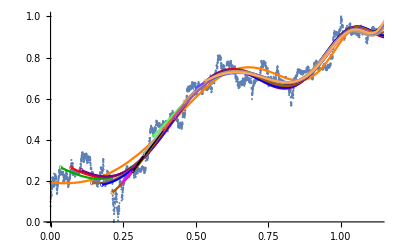

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.035461,0.070922,0.106383,0.141844,0.177305,0.212766,0.248227,0.283688,0.319149,0.35461,0.390071,0.425532,0.460993,0.496454,0.531915}

{0.00319101,0.00234031,0.00234343,0.00243879,0.0021515,0.00217522,0.00180196,0.00155479,0.0015841,0.00156862,0.00145639,0.00145638,0.00150182,0.00141554,0.00134045,0.00138837}

{10.7154,7.60836,7.36776,7.40904,6.30605,6.14282,4.89773,4.05956,3.9856,3.79292,3.36573,3.20985,3.15081,2.81834,2.5254,2.46851}

{0.0564386,0.0483322,0.0483629,0.0493354,0.0463369,0.0465898,0.0424027,0.0393856,0.0397534,0.0395568,0.0381133,0.0381107,0.038698,0.0375671,0.036554,0.0371981}

```mathematica
Export[base<>"csv/t1s.tsv", Join[{{"t1"}},T1s]]
```

/Users/mauro/Projects/bitcoin-bubbles/csv/t1s.tsv

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

3365

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

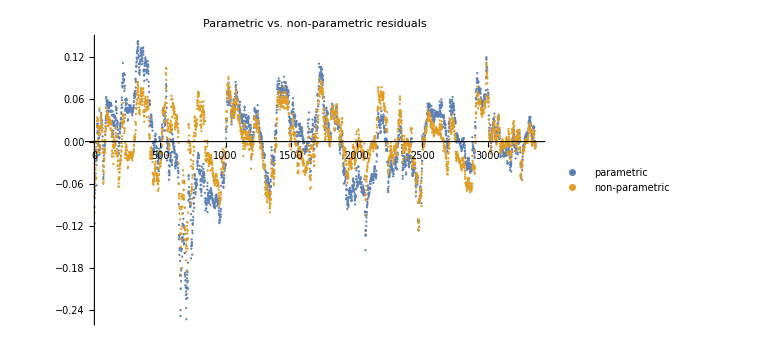

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{5.5441,10.7154}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0407159,0.056489}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.00165779,0.00319101}

```mathematica
selN=Length[T1s];
selN
```

16

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{3365,3246,3127,3008,2888,2769,2650,2530,2411,2292,2172,2053,1934,1814,1695,1576}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{3365,3246,3127,3008,2888,2769,2650,2530,2411,2292,2172,2053,1934,1814,1695,1576}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{3365,3246,3127,3008,2888,2769,2650,2530,2411,2292,2172,2053,1934,1814,1695,1576}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.00319101,0.00234031,0.00234343,0.00243879,0.0021515,0.00217522,0.00180196,0.00155479,0.0015841,0.00156862,0.00145639,0.00145638,0.00150182,0.00141554,0.00134045,0.00138837}

```mathematica
RSSs
```

{10.7154,7.60836,7.36776,7.40904,6.30605,6.14282,4.89773,4.05956,3.9856,3.79292,3.36573,3.20985,3.15081,2.81834,2.5254,2.46851}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0405951,0.0408911,0.0413511,0.0414134,0.0411679,0.0411349,0.0374468,0.0372659,0.0368301,0.0358651,0.0362628,0.0365829,0.0346834,0.034394,0.0345834,0.0337757}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.97724,σ→-0.00861049,μ→7.49047×10^-6},{ρ→0.978843,σ→-0.00836547,μ→3.13917×10^-6},{ρ→0.979701,σ→-0.00828817,μ→6.13255×10^-6},{ρ→0.978937,σ→-0.00845369,μ→-3.55915×10^-6},{ρ→0.978614,σ→-0.008467,μ→-0.0000132339},{ρ→0.979493,σ→-0.00828633,μ→-0.0000229172},{ρ→0.979611,σ→-0.00752169,μ→0.0000237453},{ρ→0.980616,σ→-0.0073005,μ→9.4231×10^-6},{ρ→0.97911,σ→-0.00748723,μ→0.0000473467},{ρ→0.979303,σ→-0.00725744,μ→0.0000314458},{ρ→0.980035,σ→-0.00720835,μ→0.0000113936},{ρ→0.979028,σ→-0.00745108,μ→0.000021496},{ρ→0.977415,σ→-0.00732775,μ→0.0000446299},{ρ→0.977361,σ→-0.00727498,μ→7.18399×10^-6},{ρ→0.978647,σ→-0.00710641,μ→0.000046144},{ρ→0.97982,σ→-0.00674896,μ→-1.15954×10^-6}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[7.49047×10^-6,{0.97724},0.0000741405],ARProcess[3.13917×10^-6,{0.978843},0.0000699811],ARProcess[6.13255×10^-6,{0.979701},0.0000686938],ARProcess[-3.55915×10^-6,{0.978937},0.0000714649],ARProcess[-0.0000132339,{0.978614},0.00007169],ARProcess[-0.0000229172,{0.979493},0.0000686633],ARProcess[0.0000237453,{0.979611},0.0000565758],ARProcess[9.4231×10^-6,{0.980616},0.0000532972],ARProcess[0.0000473467,{0.97911},0.0000560587],ARProcess[0.0000314458,{0.979303},0.0000526705],ARProcess[0.0000113936,{0.980035},0.0000519602],ARProcess[0.000021496,{0.979028},0.0000555185],ARProcess[0.0000446299,{0.977415},0.000053696],ARProcess[7.18399×10^-6,{0.977361},0.0000529253],ARProcess[0.000046144,{0.978647},0.0000505011],ARProcess[-1.15954×10^-6,{0.97982},0.0000455485]}

{11262.3,10926.5,10550.,10120.8,9696.13,9360.72,9198.01,8872.37,8446.82,8063.57,7630.35,7198.1,6792.16,6373.89,5981.86,5639.72}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

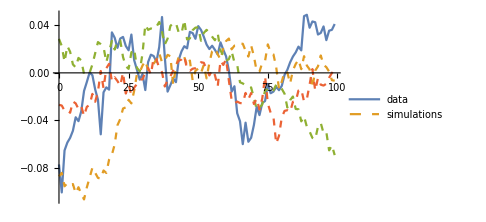
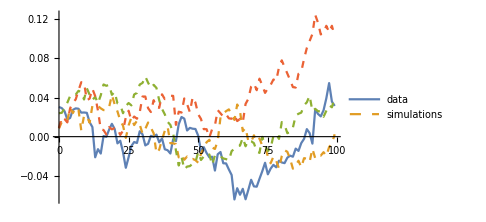
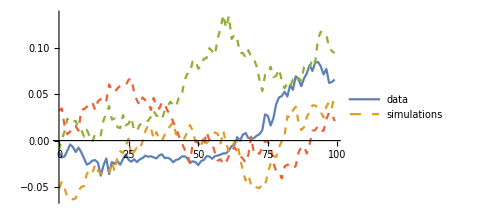
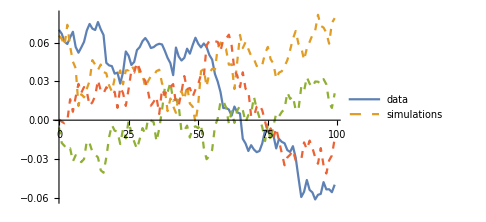
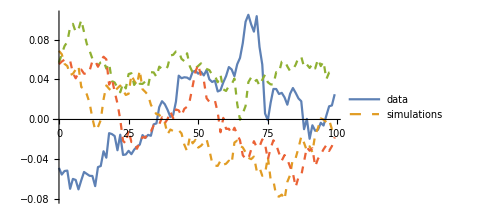
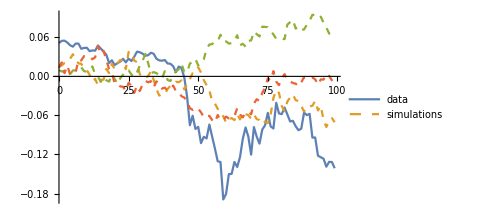
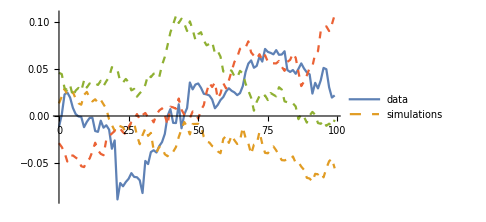
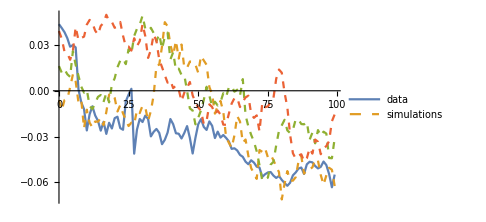

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{15.728,3344.28},{15.7417,3225.26},{15.7465,3106.26},{15.7548,2987.25},{15.7575,2867.24},{15.7309,2748.28},{15.7422,2629.26},{15.7856,2509.21},{15.7708,2390.23},{15.782,2271.21},{15.7863,2151.21},{15.8003,2032.19},{15.815,1913.17},{15.8233,1793.16},{15.8417,1674.14},{15.864,1555.11}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

3344.28

15.728

{3344.28,3225.26,3106.26,2987.25,2867.24,2748.28,2629.26,2509.21,2390.23,2271.21,2151.21,2032.19,1913.17,1793.16,1674.14,1555.11}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 4.21517 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 4.21526 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 625379 Kb

Memory Used: 3.61897 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,21,32,15,73,77,90,257,209,153,306,324,126,214,303,197}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.021,0.032,0.015,0.073,0.077,0.09,0.257,0.209,0.153,0.306,0.324,0.126,0.214,0.303,0.197}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
(* Take the first / largest that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

5

```mathematica
(* Take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
```

1.23148

```mathematica
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,minTcIndex]
```

5

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.19104,b→-0.610915,c→0.119398,d→-0.050621,T_1→0.141844,tc→1.55063,m→1.,ω→10.,RSS→6.30605,ℛerror→0.0021515,ℛσ→0.0463369,LL→9876.8,ρ→0.983354,σ→-0.00841786,μ→2.9274×10^-18,index→5}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

5

{a→1.19104,b→-0.610915,c→0.119398,d→-0.050621,T_1→0.141844,tc→1.55063,m→1.,ω→10.,RSS→6.30605,ℛerror→0.0021515,ℛσ→0.0463369,LL→9876.8,ρ→0.983354,σ→-0.00841786,μ→2.9274×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

1.

10.

1.55063

9876.8

```mathematica
t1=Subscript[T, 1]/.fit
```

0.141844

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

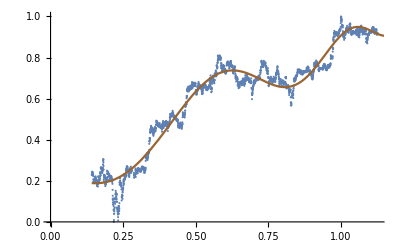

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.19104,b→-0.610915,c→0.119398,d→-0.050621,T_1→0.141844,tc→1.55063,m→1.,ω→10.,RSS→6.30605,ℛerror→0.0021515,ℛσ→0.0463369,LL→9876.8,ρ→0.983354,σ→-0.00841786,μ→2.9274×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.983354,σ→-0.00841786,μ→2.9274×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92003

{1.53637,1.55063}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92

{1.53637,1.55063,1.56838}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.125

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Fri 19 Sep 2025 13:23:49

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Sun 21 Sep 2025 08:18:02

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Tue 23 Sep 2025 13:41:23

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Thu 28 Aug 2025 04:18:02

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Sat 4 Oct 2025 16:18:02

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Tue 12 Aug 2025 08:18:02

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Tue 11 Mar 2025 00:00:00 | tc→1.23148 | Tue 12 Aug 2025 08:18:02
T_1→0.035461 | Sat 15 Mar 2025 10:40:00 | tc→1.55063 | Sun 21 Sep 2025 08:18:02
T_1→0.070922 | Wed 19 Mar 2025 21:20:00 | tc→1.59319 | Fri 26 Sep 2025 16:18:02
T_1→0.106383 | Mon 24 Mar 2025 08:00:00 | tc→1.65701 | Sat 4 Oct 2025 16:18:02
T_1→0.141844 | Fri 28 Mar 2025 18:40:00 | tc→1.55063 | Sun 21 Sep 2025 08:18:02
T_1→0.177305 | Wed 2 Apr 2025 05:20:00 | tc→1.55063 | Sun 21 Sep 2025 08:18:02
T_1→0.212766 | Sun 6 Apr 2025 16:00:00 | tc→1.35914 | Thu 28 Aug 2025 08:18:02
T_1→0.248227 | Fri 11 Apr 2025 02:40:00 | tc→1.23148 | Tue 12 Aug 2025 08:18:02
T_1→0.283688 | Tue 15 Apr 2025 13:20:00 | tc→1.23148 | Tue 12 Aug 2025 08:18:02
T_1→0.319149 | Sun 20 Apr 2025 00:00:00 | tc→1.23148 | Tue 12 Aug 2025 08:18:02
T_1→0.35461 | Thu 24 Apr 2025 10:40:00 | tc→1.27404 | Sun 17 Aug 2025 16:18:02
T_1→0.390071 | Mon 28 Apr 2025 21:20:00 | tc→1.25276 | Fri 15 Aug 2025 00:18:02
T_1→0.425532 | Sat 3 May 2025 08:00:00 | tc→1.25276 | Fri 15 Aug 2025 00:18:02
T_1→0.460993 | Wed 7 May 2025 18:40:00 | tc→1.27404 | Sun 17 Aug 2025 16:18:02
T_1→0.496454 | Mon 12 May 2025 05:20:00 | tc→1.25276 | Fri 15 Aug 2025 00:18:02
T_1→0.531915 | Fri 16 May 2025 16:00:00 | tc→1.23148 | Tue 12 Aug 2025 08:18:02

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

1.19096

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

1.18176

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
```

0.920572

```mathematica
lastPriceDate
```

2025-12-25

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1766617200&timeEnd=1766703600&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

```mathematica
latestMarketCap=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]][[5]][[2]][[7]][[2]]/10^7
```

194879.736535285

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,1}]
```

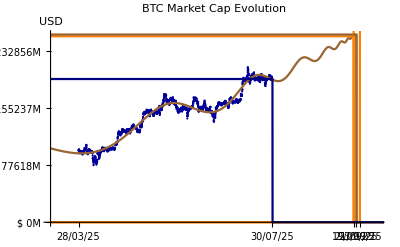

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/bitcoin-bubbles/png/BTC_MarketCapPrediction-2025-12-25.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

253045.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

255386.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
```

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

97933.4

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]
```

127011.

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

128180.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i]]},{i,min, max,50000}]
```

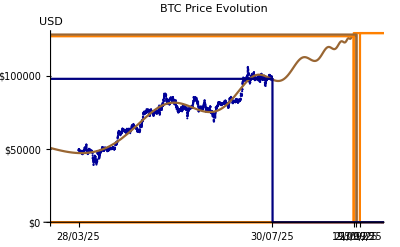

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/bitcoin-bubbles/png/BTC_PricePrediction-2025-12-25.png